# Density data plotting code

## Version: 1.0.0

## Directory setting

```mathematica
currentDir=NotebookDirectory[];
SetDirectory[currentDir];
importdir="../../python/ant/data/density/";
```

## File import

```mathematica
filename="2020122400";
hdf5File=Import[ToString@Row@{importdir,filename,".hdf5"},"Data"];
```

## Parameters

```mathematica
bincount=8;
antcount=4;
```

## Time integration

### aaa

```mathematica
imstack=hdf5File⟦1⟧;
```

```mathematica
squish=imstack⟦1⟧;
Do[
squish+=imstack⟦i⟧;
,{i,2,Length[imstack]}]
squish/=Length[imstack];
totalantness=antcount Length[imstack];
```

```mathematica
squish⟦8,8⟧=(5squish⟦8,8⟧)/6;
```

Part::partw: Part 8 of (1+$Failed)/2 does not exist.

Set::partw: Part 8 of (1+$Failed)/2 does not exist.

```mathematica
squish=squish/(Total@Total@squish);
```

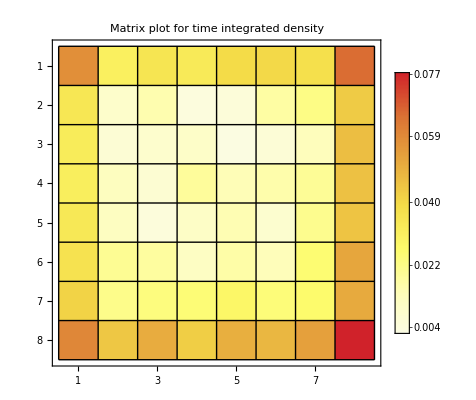

```mathematica
a=Show[MatrixPlot[squish,PlotLegends->Automatic,ColorFunction->"TemperatureMap",Mesh->True,MeshStyle->Thin,PlotLabel->"Matrix plot for time integrated density"]]
```

```mathematica
Export[ToString@Row@{filename,"out.png"},a];
```

```mathematica
(*antcount/Total[imstack⟦i⟧,{1,2}]*)
```

```mathematica
Directory[]
```

C:\Users\dlaek\Desktop\Coding\mathematica\plots

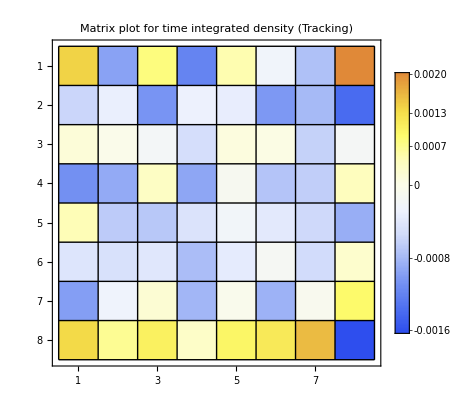

```mathematica
diff=thing-squish;out2=Show[MatrixPlot[diff,PlotLegends->Automatic,ColorFunction->"TemperatureMap",Mesh->True,MeshStyle->Thin,PlotLabel->"Matrix plot for time integrated density (Tracking)"]]
```

```mathematica
Export[ToString@Row@{filename,"diff.png"},out2]
```

2020122400diff.png

```mathematica
thingr=Reverse[thing,{1,2}];
```

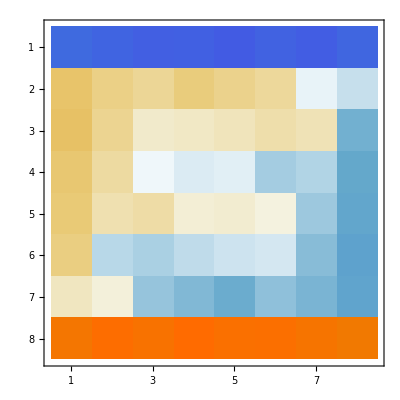

```mathematica
MatrixPlot@(thingr-thing)
```

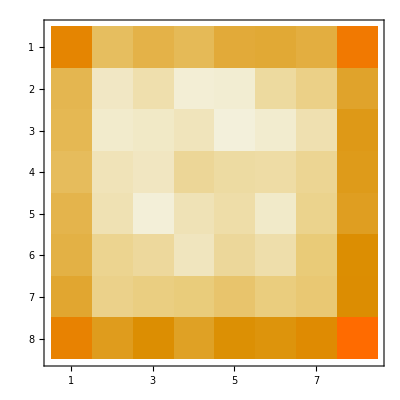

```mathematica
MatrixPlot@thing
```

```mathematica
thing⟦8,1⟧-
```

4889/108006

```mathematica
rat=diff/squish;
```

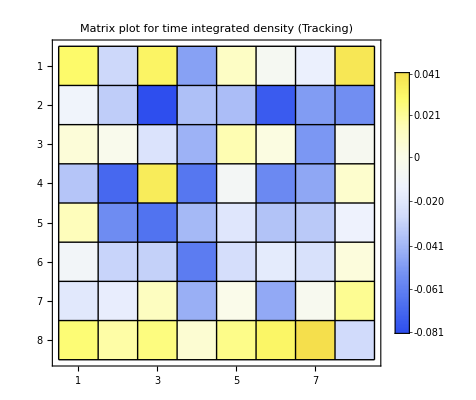

```mathematica
out3=Show[MatrixPlot[rat,PlotLegends->Automatic,ColorFunction->"TemperatureMap",Mesh->True,MeshStyle->Thin,PlotLabel->"Matrix plot for time integrated density (Tracking)"]]
```

```mathematica
Export[ToString@Row@{filename,"perdiff.png"},out3]
```

2020122400perdiff.png